```mathematica
Clear["Global`*"];
Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Import Files

```mathematica
readMatlabComplex[file_]:=ToExpression[StringSplit[StringReplace[ReadList[file,"String"],{"e"->"*10^","i"->"*I"}],","]]
```

```mathematica
allFiles=FileNames["*.csv"];
allData=readMatlabComplex[#]&/@allFiles;
```

ToExpression::sntx: Invalid syntax in or before "sampl*Ing rat*10^: 78.125 MHz".
                                                                   ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator crossov*10^r 174.6 kHz".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator saturat*Ion +43.0 dB".
                                                  ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

```mathematica
numoffiles=Dimensions[allFiles][[1]];
index=Table[i,{i,1,numoffiles}];
fileswithindex=Thread[{index,allFiles}];
dataset=Table[allData[[i]][[19;;]],{i,1,numoffiles}];
numset=Table[Dimensions[dataset[[i]]][[1]],{i,1,numoffiles}];
fileswithindex
```

{{1,100100P_20230417_201152_HighResData.csv},{2,100100X_20230417_201126_HighResData.csv},{3,LPam0pm_10_20230412_214245_HighResData.csv},{4,LPam_10pm0_20230412_213845_HighResData.csv},{5,Lpamoffpmoff_20230412_212225_HighResData.csv},{6,LXam0pm_10_20230412_214340_HighResData.csv},{7,LXam_10pm0_20230412_213812_HighResData.csv},{8,LXamoffpmoff_20230412_212345_HighResData.csv},{9,offoffP2_20230417_201024_HighResData.csv},{10,offoffX2_20230417_201057_HighResData.csv}}

## Density matrix in Fock basis

```mathematica
bin=320; (*Dimension of Discretized quadrature value Better be even?*)
n=8;  (*Photon number cutoff*)
dim=n+1; (*Dimension of density matrix*)

(*Ensuring positive semidefiniteness, trace property*)
rr=LowerTriangularize[Array[Subscript[r,##]&,{dim,dim}]];
ii=LowerTriangularize[Array[Subscript[im,##]&,{dim,dim}]];
ii=ii-DiagonalMatrix[Diagonal[ii]];
ii=ⅈ*ii;
t=rr+ii;
(*Density Matrix*)
ρ= ConjugateTranspose[t] . t/Tr[ConjugateTranspose[t] . t] ;
```

## Fock State Wave Function

```mathematica
fn=16;(*Pre-caculation*) 
psi[m_,x_]=HermiteH[m,x]/(√(2^m m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
Tpsi=Table[psi[m,x],{m,0,fn}];
```

## Shot Noise Unit Estimation

```mathematica
size1=Dimensions[allData[[9]][[19;;]]];
size1=size1[[1]];
vacp=Table[allData[[9]][[19;;]][[i]][[2]],{i,1,size1}];
snu1=StandardDeviation[vacp]
mp=Mean[vacp]

size2=Dimensions[allData[[10]][[19;;]]];
size2=size2[[1]];
vacx=Table[allData[[10]][[19;;]][[i]][[2]],{i,1,size2}];
snu2=StandardDeviation[vacx]
mx=Mean[vacx]
(*Shot noise unit is manually fit to match vacuum data with our theoretical expectation*)
snu=(snu1+snu2)/1.5;
```

4.86853×10^-6

-0.0000116228

4.88555×10^-6

-0.0000116536

## Discretizing Phase Space of the Signal

```mathematica
(*slice=snu*n/(bin/2);
xevent=ConstantArray[0,bin+1];
pevent=ConstantArray[0,bin+1];
(*63*)
(*X-Quadrature of the Data*)
xsize=Dimensions[allData[[6]][[19;;]]];
xsize=xsize[[1]];
xquad=Table[allData[[6]][[19;;]][[i]][[2]],{i,1,xsize}];

(*P-Quadrature of the Data*)
psize=Dimensions[allData[[3]][[19;;]]];
psize=psize[[1]];
pquad=Table[allData[[3]][[19;;]][[i]][[2]],{i,1,psize}];*)
```

## Phase Squeezed state generation

```mathematica
slice=snu*n/(bin/2);
(*hbar=1*)
(*squeezing parameter r*)
r=0.5;
α=1.5;
plusx[x_]=Exp[(-(x-α)^2)/(2*Exp[2*r])];
plusp[x_]=Exp[(-(x-α)^2)/(2*Exp[2*r])];
```

## Squeezed state Event

```mathematica
xevent=Table[(plusx[(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
xnorm=Sum[xevent[[i]],{i,1,bin+1}];
xnorm//N
xevent=xevent/xnorm;
pevent=Table[(plusp[(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
pnorm=Sum[pevent[[i]],{i,1,bin+1}];
pnorm//N
pevent=pevent/pnorm;
```

58.4456

58.4456

## Counting Events

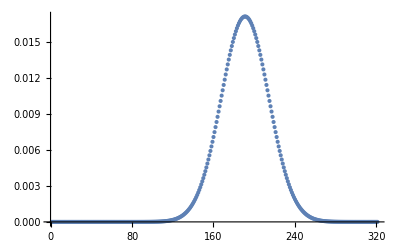

-Graphics-

```mathematica
(*(*Counting Occurence*)
For[i=1,i<xsize+1,i++,
xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]=xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]+1;]

For[i=1,i<psize+1,i++,
pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]=pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]+1;]

(*Normalization*)
xevent=xevent/xsize;
pevent=pevent/psize;*)

(*Gmn is imported, discretized and normalized occurence of event*)
G={xevent,pevent}//N;
ListPlot[xevent, PlotRange->Full]
ListPlot[pevent,PlotRange->Full]
```

## Normalization Parameter for Projector

```mathematica
hermite0=Table[(psi[0,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm=Sum[hermite0[[i]],{i,1,bin+1}];
norm//N
hermite0=hermite0/norm;
```

20.

## Projector Represented in quadrature basis

```mathematica
(*Matrix Element in Fock basis*)
Π=Table[(Tpsi[[a+1]]Tpsi[[b+1]]/norm)ⅇ^(ⅈ(b-a)θ),{a,0,n},{b,0,n}] ;
```

## Discretize X and θ

```mathematica
theta={0,Pi/2};
quad=Subdivide[-n,n,bin];
```

## Deviation Function

```mathematica
Q=Re[
Sum[(      G[[j,i]]-(  Tr[Π.ρ]/.{x->quad[[i]],θ->theta[[j]]}  )   )^2,{i,1,bin+1},{j,1,2}]
];
```

## Optimization Kernel

```mathematica
flat1=DeleteCases[Flatten[rr],_Integer];
flat2=DeleteCases[Flatten[-ⅈ*ii],_Integer];
kernel=Join[flat1,flat2];
```

## Maximum Entropy reconstruction

```mathematica
solution=FindMinimum[Q,kernel];

Chop[ρ /. solution[[2]] ];

Chop[MatrixForm[ρ /. solution[[2]]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(0.127555 | 0.0903933+0.0741555 ⅈ | 0.0182253+0.0900441 ⅈ | -0.0371877+0.0543417 ⅈ | -0.0358516+0.0188834 ⅈ | -0.0270333-0.0000140828 ⅈ | -0.0193845-0.022809 ⅈ | -0.00211031-0.0288527 ⅈ | 0.00932746-0.0189759 ⅈ
0.0903933-0.0741555 ⅈ | 0.136296 | 0.0956919+0.100837 ⅈ | -0.0132748+0.113583 ⅈ | -0.0422425+0.0446646 ⅈ | -0.0195704+0.0156818 ⅈ | -0.0185059+0.00374509 ⅈ | -0.0144385-0.00926895 ⅈ | -0.00481306-0.013121 ⅈ
0.0182253-0.0900441 ⅈ | 0.0956919-0.100837 ⅈ | 0.18842 | 0.120775+0.139758 ⅈ | -0.0063091+0.11483 ⅈ | -0.0182709+0.0310149 ⅈ | 0.00316511+0.0030042 ⅈ | 0.00716646+0.00256625 ⅈ | 0.00296781+0.003193 ⅈ
-0.0371877-0.0543417 ⅈ | -0.0132748-0.113583 ⅈ | 0.120775-0.139758 ⅈ | 0.206898 | 0.102758+0.10735 ⅈ | 0.00762289+0.0569734 ⅈ | 0.000570934-0.000902403 ⅈ | 0.0134351-0.0104545 ⅈ | 0.0141783-0.00260365 ⅈ
-0.0358516-0.0188834 ⅈ | -0.0422425-0.0446646 ⅈ | -0.0063091-0.11483 ⅈ | 0.102758-0.10735 ⅈ | 0.131849 | 0.0549912+0.0488441 ⅈ | -0.00156617+0.0238228 ⅈ | -0.00874541-0.00428036 ⅈ | 0.0006556-0.0135682 ⅈ
-0.0270333+0.0000140828 ⅈ | -0.0195704-0.0156818 ⅈ | -0.0182709-0.0310149 ⅈ | 0.00762289-0.0569734 ⅈ | 0.0549912-0.0488441 ⅈ | 0.0664415 | 0.0331181+0.0328852 ⅈ | -0.000696642+0.0261942 ⅈ | -0.0149065+0.00547254 ⅈ
-0.0193845+0.022809 ⅈ | -0.0185059-0.00374509 ⅈ | 0.00316511-0.0030042 ⅈ | 0.000570934+0.000902403 ⅈ | -0.00156617-0.0238228 ⅈ | 0.0331181-0.0328852 ⅈ | 0.0606017 | 0.0370174+0.0308553 ⅈ | 0.000701822+0.0306769 ⅈ
-0.00211031+0.0288527 ⅈ | -0.0144385+0.00926895 ⅈ | 0.00716646-0.00256625 ⅈ | 0.0134351+0.0104545 ⅈ | -0.00874541+0.00428036 ⅈ | -0.000696642-0.0261942 ⅈ | 0.0370174-0.0308553 ⅈ | 0.0473145 | 0.0255539+0.0226007 ⅈ
0.00932746+0.0189759 ⅈ | -0.00481306+0.013121 ⅈ | 0.00296781-0.003193 ⅈ | 0.0141783+0.00260365 ⅈ | 0.0006556+0.0135682 ⅈ | -0.0149065-0.00547254 ⅈ | 0.000701822-0.0306769 ⅈ | 0.0255539-0.0226007 ⅈ | 0.0346252)

## Plotting Real part of Density Matrix

```mathematica
DiscretePlot3D[Abs@Re[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Plotting Imaginary part

```mathematica
DiscretePlot3D[Abs@Im[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Wigner Reconstruction

```mathematica
g=2;
M=4;
xrange={-5,5};
yrange={-5,5};
linespace=100;
rho=ρ /. solution[[2]];
%//MatrixForm;
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
{xx,yy}=meshgrid[Array[#&,linespace,xrange],Array[#&,linespace,yrange]];
aa=0.5*g*(xx+ⅈ yy);
%//MatrixForm;
wlist=Table[Table[Table[0,{i,1,M}],{j,1,M}],{k,1,M}];
wlist[[1]]=Exp[-2 Abs[aa]^2]/π;
W=Re[rho[[1,1]]]*Re[wlist[[1]]];

For[nn=1, nn<M,nn++,
wlist[[nn+1]]=(2.0*aa*wlist[[nn]])/√nn;
W+=2*Re[rho[[1,nn+1]]*wlist[[nn+1]]];
]


For[mm=1, mm<M,mm++,

temp=wlist[[mm+1]];
wlist[[mm+1]]=(2*Conjugate[aa]*temp-√mm*wlist[[mm]])/√mm;
W+=Re[rho[[mm+1,mm+1]]*wlist[[mm+1]]];
For[nn=mm+1, nn<M,nn++,
temp2=(2*aa*wlist[[nn]]-√mm*temp)/√nn;
temp=wlist[[nn+1]];
wlist[[nn+1]]=temp2;
W+=2*Re[rho[[mm+1,nn+1]]*wlist[[nn+1]]];
]
]
list=0.5*W*g^2;
pos=Position[list,_?(#==Max[list]&)]
disp=Sqrt[((50-pos[[1,1]])/10)^2+((50-pos[[1,2]])/10)^2]//N
ListPlot3D[0.5*W*g^2,PlotRange->All, Boxed->False,DataRange->{{-5,5},{-5,5}}]
```

{{42,60}}

1.28062

-Graphics3D-